## Конечные цепи Маркова: Алгоритм PageRank

### Зададим граф сайта по существующим ссылкам на страницы

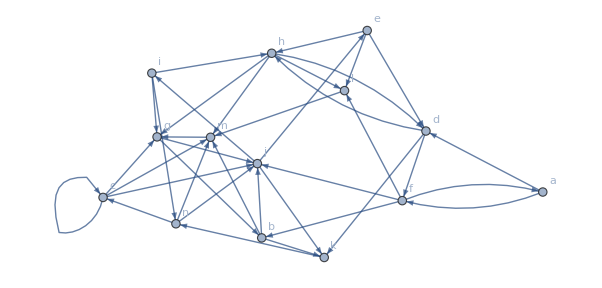

```mathematica
Clear["Global`*"]
edge={a->d,a->f,b->j,b->k,b->m,c->c,c->g,c->j,c->m,d->f,d->h,d->k,e->d,e->h,e->l,f->a,f->b,f->j,f->l,g->b,g->j,h->d,h->g,h->l,h->m,i->g,i->h,i->n,j->e,j->i,j->k,k->n,l->m,m->g,n->c,n->j,n->m};
G=Graph[edge,VertexLabels->"Name"]
```

### Алгоритм на графе PageRankCentrality

```mathematica
prg=PageRankCentrality[G,0.85]
hprg=HighlightGraph[G,VertexList[G],VertexSize->Thread[VertexList[G]->Rescale[prg]]]
sprg=SortBy[Transpose[{VertexList[G], prg}],Last];
%//TableForm
```

{0.0171563,0.0434461,0.0303155,0.0803094,0.141805,0.0859565,0.119438,0.0385367,0.148596,0.051863,0.0508924,0.0425967,0.0508924,0.0981967}

-Graphics-

a | 0.0171563
f | 0.0303155
c | 0.0385367
l | 0.0425967
d | 0.0434461
e | 0.0508924
i | 0.0508924
h | 0.051863
b | 0.0803094
k | 0.0859565
n | 0.0981967
m | 0.119438
j | 0.141805
g | 0.148596

### Алгоритм на графе PageRank на основе цепей Маркова

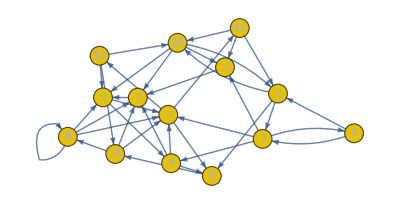

{0.00291071,0.0305625,0.0116429,0.0832646,0.159362,0.0910629,0.119515,0.0483421,0.160708,0.0456012,0.0531205,0.0320179,0.0531205,0.10877}

-Graphics-

a | 0.00291071
f | 0.0116429
d | 0.0305625
l | 0.0320179
h | 0.0456012
c | 0.0483421
i | 0.0531205
e | 0.0531205
b | 0.0832646
k | 0.0910629
n | 0.10877
m | 0.119515
j | 0.159362
g | 0.160708

```mathematica
mt=Normal[AdjacencyMatrix[G]];
mt//MatrixForm;
mat=#/Total[#]&/@ mt;

proc1=DiscreteMarkovProcess[1,mat//N];
MarkovProcessProperties[proc1];
Graph[proc1]
pr=Table[Probability[x==i,x\[Distributed]StationaryDistribution[proc1]],{i,1,14}]

hpr=HighlightGraph[G,VertexList[G],VertexSize->Thread[VertexList[G]->Rescale[pr]]]
spr=SortBy[Transpose[{VertexList[G], pr}],Last];
%//TableForm
```

### Сравнеие PageRankCentrality и PageRank

```mathematica
{{Grid[sprg,Frame->All,Background->{None,{3->Pink}}],Grid[spr,Frame->All,Background->{None,{3->Pink}}]}}//TableForm
```

a | 0.0171563
f | 0.0303155
c | 0.0385367
l | 0.0425967
d | 0.0434461
e | 0.0508924
i | 0.0508924
h | 0.051863
b | 0.0803094
k | 0.0859565
n | 0.0981967
m | 0.119438
j | 0.141805
g | 0.148596 | a | 0.00291071
f | 0.0116429
d | 0.0305625
l | 0.0320179
h | 0.0456012
c | 0.0483421
i | 0.0531205
e | 0.0531205
b | 0.0832646
k | 0.0910629
n | 0.10877
m | 0.119515
j | 0.159362
g | 0.160708

```mathematica
{{hprg,hpr}}//TableForm
```

-Graphics-